```mathematica
Remove["Global`*"]
```

## Parameters

```mathematica
Nmax = 7; 
α = 1./2.*(1 - Tanh[-3/2.])(*γ300 2.18/1000*) (*γ500 2.47/1000*) (*γ1300 3.54*);
β = 1./2.*(1 - Tanh[3/2.])(*γ300 3.96/1000*) (*γ500 1.57/1000*) (*γ1300 3.54*);
```

## Markov Equation of the Langmuir kinetics

#### Birth & death rate of occupancy state k

```mathematica
SubPlus[Ω][k_]:=α *(Nmax-k);
SubMinus[Ω][k_]:=β *k
```

```mathematica
Table[SubPlus[Ω][k],{k,0,Nmax}]
Table[SubMinus[Ω][k],{k,0,Nmax}]
```

{6.66802,5.71544,4.76287,3.8103,2.85772,1.90515,0.952574,0.}

{0.,0.0474259,0.0948517,0.142278,0.189703,0.237129,0.284555,0.331981}

#### Stochastic matrix

```mathematica
rowStart={-(SubPlus[Ω][0]),SubMinus[Ω][1], ConstantArray[0,{1,Nmax-1}]}//Flatten;
middle=Table[{ConstantArray[0,{1,k-1}]//Flatten,{SubPlus[Ω][k-1], -(SubPlus[Ω][k]+SubMinus[Ω][k]), SubMinus[Ω][k+1]}, ConstantArray[0,{1,Nmax-(k+1)}]//Flatten}//Flatten,{k,1,Nmax-1}] ;
rowEnd={ConstantArray[0,{1,Nmax-1}],SubPlus[Ω][Nmax-1], -(SubMinus[Ω][Nmax])}//Flatten;
(A=Join[{rowStart}, middle,{rowEnd}])//MatrixForm
DiagonalizableMatrixQ[A]
```

(-6.66802 | 0.0474259 | 0 | 0 | 0 | 0 | 0 | 0
6.66802 | -5.76287 | 0.0948517 | 0 | 0 | 0 | 0 | 0
0 | 5.71544 | -4.85772 | 0.142278 | 0 | 0 | 0 | 0
0 | 0 | 4.76287 | -3.95257 | 0.189703 | 0 | 0 | 0
0 | 0 | 0 | 3.8103 | -3.04743 | 0.237129 | 0 | 0
0 | 0 | 0 | 0 | 2.85772 | -2.14228 | 0.284555 | 0
0 | 0 | 0 | 0 | 0 | 1.90515 | -1.23713 | 0.331981
0 | 0 | 0 | 0 | 0 | 0 | 0.952574 | -0.331981)

True

```mathematica
Total[A,{1}]//Chop
```

{0,0,0,0,0,0,0,0}

```mathematica
Eigenvectors[A]//MatrixForm;
Eigenvalues[A]//Chop
```

{-7.,-6.,-5.,-4.,-3.,-2.,-1.,0}

```mathematica
(U = Transpose[Eigenvectors[A]])//MatrixForm;
(Ui=Inverse[U])//MatrixForm;
```

```mathematica
Λ=Ui.A.U//Chop//MatrixForm
```

(-7. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -6. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -5. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -4. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Solution of the decoupled system of linear ODEs

```mathematica
solDiago[t_]:=Table[c[k]*Exp[Eigenvalues[A][[k]]*t],{k,1,Length[A]}]
```

```mathematica
solDiago[t]//Chop//MatrixForm;
```

#### Solution of the original system of linear ODEs

```mathematica
(solOri=U.solDiago[t])//MatrixForm;
```

#### Initial conditions

```mathematica
(IC=solOri/. t-> 0)//MatrixForm;
```

#### Find special solution equivalent to resurrection

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]];
```

```mathematica
solSpecial = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecial[[k]],{k,1,Length[solSpecial]}]/.t->100
```

General::munfl: 3.55271×10^-14 9.85968×10^-305 is too small to represent as a normalized machine number; precision may be lost.

1.

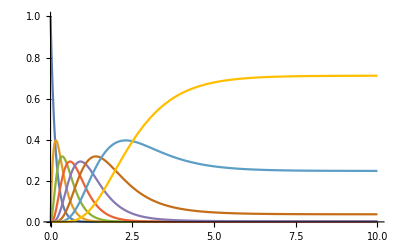

```mathematica
Tmax=10;
Plot[{solSpecial},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

#### Find special solution equivalent to release after stall

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==Nmax+1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]];
```

```mathematica
solSpecialStall = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecialStall[[k]],{k,1,Length[solSpecial]}]/.t->100
```

General::munfl: -2.64698×10^-23 9.85968×10^-305 is too small to represent as a normalized machine number; precision may be lost.

1.

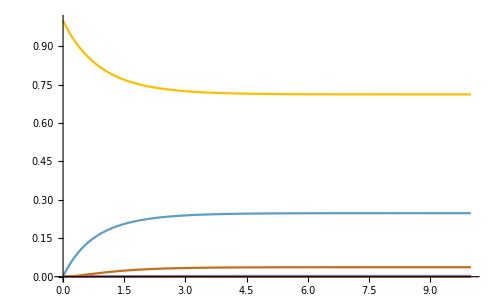

```mathematica
Tmax=10;
Plot[{solSpecialStall},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

#### Stationary solution

```mathematica
solSpecial/. t-> 100000//MatrixForm
```

General::munfl: Exp[-700000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-600000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(5.39644×10^-10
7.58733×10^-8
4.57187×10^-6
0.000153047
0.00307404
0.0370462
0.248031
0.711691)

```mathematica
Manipulate[DiscretePlot[solSpecial[[k]]/. t-> T,{k,1,Nmax},ExtentSize->1],{T,0.01,100,1}]
```

#### Mean occupancy for resurrection

```mathematica
m[t_]:=Sum[solSpecial[[k]]*(k-1),{k,1,Length[solSpecial]}]
```

#### Standard Deviation resurrection

```mathematica
sd[t_]:=Sqrt[Sum[solSpecial[[k]]*(k-1)^2,{k,1,Length[solSpecial]}]-m[t]^2]
```

#### Mean occupancy for stall

```mathematica
mStall[t_]:=Sum[solSpecialStall[[k]]*(k-1),{k,1,Length[solSpecialStall]}]
```

#### Standard Deviation stall

```mathematica
sdStall[t_]:=Sqrt[Sum[solSpecialStall[[k]]*(k-1)^2,{k,1,Length[solSpecialStall]}]-mStall[t]^2]
```

#### Plots

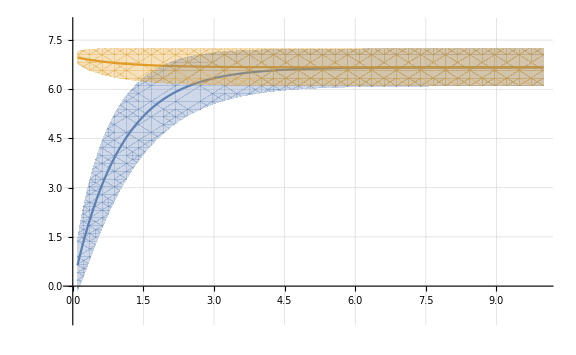

```mathematica
Tmax=10;
plot=Show[Plot[{m[t],mStall[t]},{t,0.1,Tmax},PlotRange->{{0,Tmax},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes",ImageSize->Large],
RegionPlot[{m[t]-sd[t]<y && y<m[t]+sd[t],mStall[t]-sdStall[t]<y && y<mStall[t]+sdStall[t]},{t,0.1,Tmax},{y,-1,Nmax+1},BoundaryStyle->{Dotted,Thickness[0]}]]
```

```mathematica
m[t] /. t-> 1000
```

General::munfl: Exp[-7000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

6.66802

## Dwell time: zero occupancy

```mathematica
p=Table[k*(β-α)+α*Nmax,{k,0,Nmax}];
λ=-Log[1-p]
```

{-1.73484-3.14159 ⅈ,-1.56085-3.14159 ⅈ,-1.35008-3.14159 ⅈ,-1.08268-3.14159 ⅈ,-0.716583-3.14159 ⅈ,-0.133024-3.14159 ⅈ,1.43915-3.14159 ⅈ,0.403439}